```mathematica
Needs["PlotLegends`"]
```

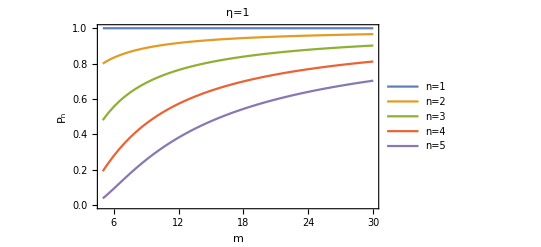

```mathematica
Plot[{Binomial[m,n]n!(1/m)^n /. n->1,Binomial[m,n]n!(1/m)^n /. n->2,Binomial[m,n]n!(1/m)^n /. n->3,Binomial[m,n]n!(1/m)^n /. n->4,Binomial[m,n]n!(1/m)^n /. n->5},{m,5,30},BaseStyle->{FontSize->14},Frame->True,FrameLabel->{"m","P_n"},PlotLabel->"η=1",PlotLegends->{"n=1","n=2","n=3","n=4","n=5"}]
```